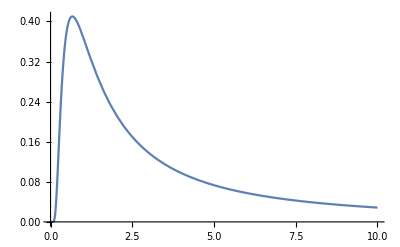

```mathematica
Plot[Exp[-1/x]/x^(3/2),{x,0,10}]
```

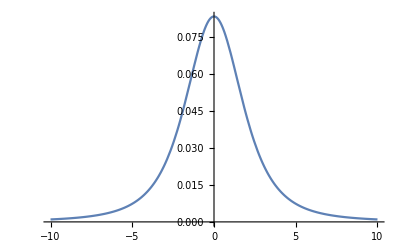

```mathematica
Plot[(Exp[2x]-1-2x*Exp[x])/(Exp[x]+1)^2/x^3,{x,-10,10}]
```

```mathematica
f[x_]=(Exp[2x]-1-2x*Exp[x])/(Exp[x]+1)^2/x^3;
```

```mathematica
NIntegrate[f[x],{x,-∞,∞}]
```

0.426278

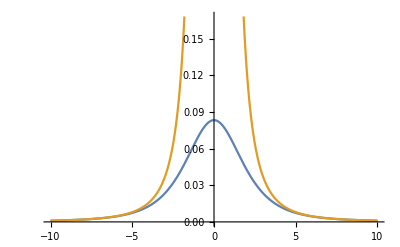

```mathematica
Plot[{f[x], 1/Abs[x]^3},{x,-10,10}]
```

```mathematica
Series[1/T^2,{T,Tc,2}]
```

1/Tc^2-(2 (T-Tc))/Tc^3+(3 (T-Tc)^2)/Tc^4+O[T-Tc]^3

```mathematica
Integrate[Exp[x]*(Exp[x]-1)/(Exp[x]+1)^3/x,{x,-∞,∞}]
```

-14 Zeta'[-2]

```mathematica
N[-14 Zeta'[-2]]
```

0.426278